## 2D Steady flow over bottom topography (depth projected)

This notebook repeats a single experiment and uses a different reduced system for the solution in each repetition. The parameters shallowness and Froude number are fixed. The plots allow for a direct comparison of how flow variables are modeled by the different systems. The variables we study are the height, the means of velocities and the nonhydrostatic pressure and the respective moments up to third order.

## Preliminaries

```mathematica
(* clear the scope *)
Quiet[Remove["Global`*"];
Remove/@((#<>"*")&/@Contexts[Evaluate[Context[]]]);]
```

```mathematica
(* set directory of the engine folder *)
engineDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"engine"}];
```

```mathematica
(* load engines *)
Get[FileNameJoin[{engineDirectory,"FreeSurf.wl"}]] 
Get[FileNameJoin[{engineDirectory,"DSM0.wl"}]] 
Get[FileNameJoin[{engineDirectory,"DSM1.wl"}]] 
Get[FileNameJoin[{engineDirectory,"DSM2.wl"}]] 
Get[FileNameJoin[{engineDirectory,"DSM3.wl"}]] 
Get[FileNameJoin[{engineDirectory,"GN.wl"}]] 

(* some option for nicer plots *)
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"];
```

```mathematica
(* set up plotting environment*)
plotHeight=170;labelHeight=17;
Clear[pRange];
defaultPlotOptions=Options[#]&/@{Plot,ListPlot}; (*save default for restoring later*)
SetOptions[#,
ImageSize->{Automatic,plotHeight},
ImagePadding->{{70,50},{40,25}},
AspectRatio->1/2,
PlotRangePadding->None,
Frame->None,
Axes->None,
LabelStyle->Directive[Black,14],
PlotRangeClipping->True,
GridLines->None,
PlotRange->pRange
];& /@{Plot,ListPlot};

SetOptions[ListPlot,PlotStyle->Black,PlotMarkers->{"∘",28}];
SetOptions[Plot, PlotTheme->{"BoldColor"}];

niceBlue=ColorData[97,1]; fillingBlue=Directive[Opacity[0.2],niceBlue];niceGreen=ColorData[97,3];
```

## Set experiment parameters

```mathematica
Fr = .6; H = .4; n = 90;η=.09; σ=.25;
```

## Run simulation

```mathematica
{dsm0, dsm1, dsm2, dsm3, full, gn} = (#[H, Fr,η,σ, n]) & /@ {DSM0, DSM1, DSM2, DSM3, FreeSurf, GN};
```

```mathematica
allDataLoaded[]:=AllTrue[((h[0] /.#)&/@ {dsm0,dsm1,dsm2,dsm3,full,gn}),NumericQ];
(*check if all data is there loaded*)
Clear[abort];If[!allDataLoaded[],abort=!ChoiceDialog["Some functions seem to be missing! Continue?"]];If[abort,Interrupt[],Nothing];
```

## Height and means

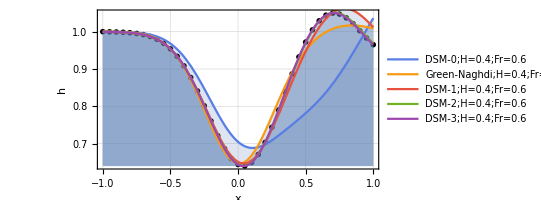

```mathematica
pRange=Automatic; (* you can play with the plot range here or use wolfram's automatic range determination*)

plotHFull=ListPlot[Table[{x,h[x]/.full},{x,-1,1,.05}],PlotLegends->Placed[tag/.full,Right],
FrameLabel->{x,h},Frame->True,GridLines->Automatic];
plotHMoments=Plot[Evaluate[h[x] /. #& /@{dsm0,gn,dsm1,dsm2,dsm3}],{x,-1,1},Filling->Axis,FillingStyle->fillingBlue,PlotLegends->Placed[tag/.#&/@{dsm0,gn,dsm1,dsm2,dsm3},Right]];
plotH=Show[plotHFull,plotHMoments]
```

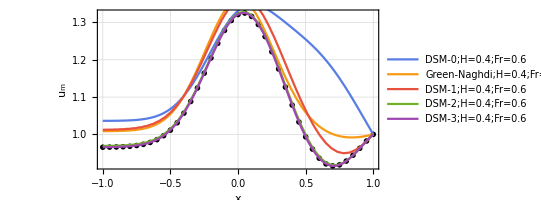

```mathematica
pRange=Automatic;;

plotUmFull=ListPlot[Table[{x,um[x]/.full},{x,-1,1,.05}],GridLines->Automatic,Frame->True,PlotLegends->Placed[tag /.full,Right],FrameLabel->{x,Subscript[u,m]}];
plotUmMoments=Plot[Evaluate[um[x]/.#& /@{dsm0,gn,dsm1,dsm2,dsm3}],{x,-1,1},PlotLegends->Placed[tag/.#&/@{dsm0,gn,dsm1,dsm2,dsm3},Right]];
plotUm=Show[plotUmFull,plotUmMoments]
```

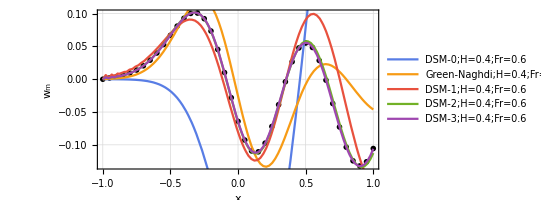

```mathematica
pRange=Automatic;;

plotWmFull=ListPlot[Table[{x,wm[x]/.full},{x,-1,1,.05}],GridLines->Automatic,Frame->True,PlotLegends->Placed[tag /.full,Right],FrameLabel->{x,Subscript[w,m]}];
plotWmMoments=Plot[Evaluate[wm[x]/.#&/@{dsm0,gn,dsm1,dsm2,dsm3}],{x,-1,1},PlotLegends->Placed[tag/.#&/@{dsm0,gn,dsm1,dsm2,dsm3},Right]];
plotWm=Show[plotWmFull,plotWmMoments]
```

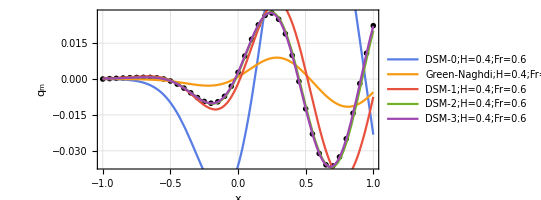

```mathematica
pRange=Automatic;

plotQmFull=ListPlot[Table[{x,qm[x]/.full},{x,-1,1,.05}],GridLines->Automatic,Frame->True,PlotLegends->Placed[tag/.full,Right],FrameLabel->{x,Subscript[q,m]}];
plotQmMoments=Plot[Evaluate[qm[x]/.#&/@{dsm0,gn,dsm1,dsm2,dsm3}],{x,-1,1},PlotLegends->Placed[tag/.#&/@{dsm0,gn,dsm1,dsm2,dsm3},Right]];
plotQm=Show[plotQmFull,plotQmMoments]
```

## First order moments

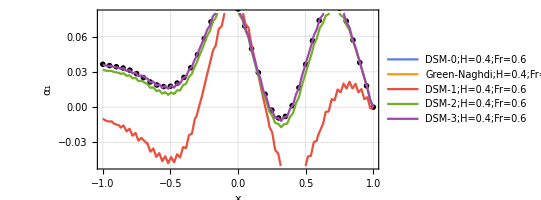

```mathematica
pRange={-.05,.08};
plotAlpha1Full=ListPlot[Table[{x,alpha1[x] /. full},{x,-1,1,.05}],GridLines->Automatic,Frame->True,PlotLegends->Placed[tag /.full,Right],FrameLabel->{x,Subscript[α,1]}];
plotAlpha1Moments=Plot[Evaluate[alpha1[x]/.#&/@{dsm0,gn,dsm1,dsm2,dsm3}],{x,-1,1},PlotLegends->Placed[tag /.#&/@{dsm0,gn,dsm1,dsm2,dsm3},Right]];
plotAlpha1=Show[plotAlpha1Full,plotAlpha1Moments]
```

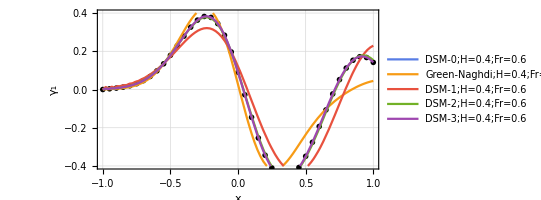

```mathematica
pRange={-.4,.4};
plotGamma1Full=ListPlot[Table[{x,gamma1[x]/.full},{x,-1,1,.05}],GridLines->Automatic,Frame->True,PlotLegends->Placed[tag /.full,Right],FrameLabel->{x,Subscript[γ,1]}];
plotGamma1Moments=Plot[Evaluate[gamma1[x]/.#&/@{dsm0,gn,dsm1,dsm2,dsm3}],{x,-1,1},PlotLegends->Placed[tag /.#&/@{dsm0,gn,dsm1,dsm2,dsm3},Right]];
plotGamma1=Show[plotGamma1Full,plotGamma1Moments]
```

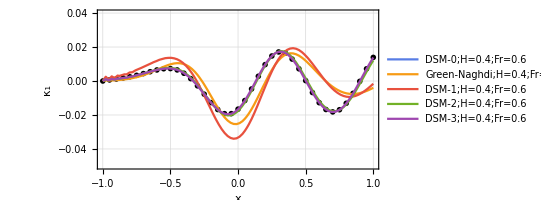

```mathematica
pRange={-.05,.04};
plotKappa1Full=ListPlot[Table[{x,kappa1[x]/.full},{x,-1,1,.05}],GridLines->Automatic,Frame->True,PlotLegends->Placed[tag/.full,Right],FrameLabel->{x,Subscript[κ,1]}];
plotKappa1Moments=Plot[Evaluate[kappa1[x]/.#&/@{dsm0,gn,dsm1,dsm2,dsm3}],{x,-1,1},PlotLegends->Placed[tag/.#&/@{dsm0,gn,dsm1,dsm2,dsm3},Right]];
plotKappa1=Show[plotKappa1Full,plotKappa1Moments]
```

## Second order moments

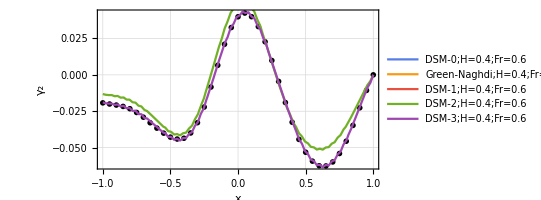

```mathematica
pRange=Automatic;

plotAlpha2Full=ListPlot[Table[{x,alpha2[x]/.full},{x,-1,1,.05}],GridLines->Automatic,Frame->True,PlotLegends->Placed[tag/.full,Right],FrameLabel->{x,Subscript[γ,2]}];
plotAlpha2Moments=Plot[Evaluate[alpha2[x]/.#&/@{dsm0,gn,dsm1,dsm2,dsm3}],{x,-1,1},PlotLegends->Placed[tag/.#&/@{dsm0,gn,dsm1,dsm2,dsm3},Right]];
plotAlpha2=Show[plotAlpha2Full,plotAlpha2Moments]
```

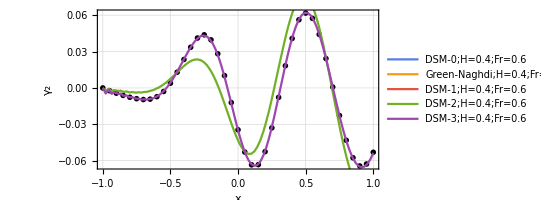

```mathematica
pRange=Automatic;

plotGamma2Full=ListPlot[Table[{x,gamma2[x]/.full},{x,-1,1,.05}],GridLines->Automatic,Frame->True,PlotLegends->Placed[tag/.full,Right],FrameLabel->{x,Subscript[γ,2]}];
plotGamma2Moments=Plot[Evaluate[gamma2[x]/.#&/@{dsm0,gn,dsm1,dsm2,dsm3}],{x,-1,1},PlotLegends->Placed[tag/.#&/@{dsm0,gn,dsm1,dsm2,dsm3},Right]];
plotGamma2=Show[plotGamma2Full,plotGamma2Moments]
```

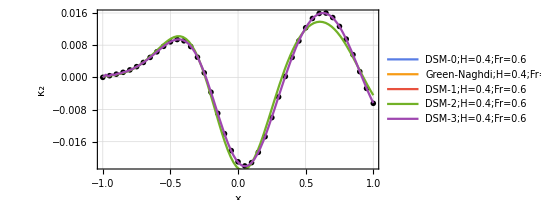

```mathematica
pRange=Automatic;

plotKappa2Full=ListPlot[Table[{x,kappa2[x]/.full},{x,-1,1,.05}],GridLines->Automatic,Frame->True,PlotLegends->Placed[tag/.full,Right],FrameLabel->{x,Subscript[κ,2]}];
plotKappa2Moments=Plot[Evaluate[kappa2[x]/. #&/@{dsm0,gn,dsm1,dsm2,dsm3}],{x,-1,1},PlotLegends->Placed[tag/. #&/@{dsm0,gn,dsm1,dsm2,dsm3},Right]];
plotKappa2=Show[plotKappa2Full,plotKappa2Moments]
```